# Convergence Rates

We need to make sure people have a clear understanding of convergence rates and their practical importance.

## 1D Root finding

We are going to use 1D foot finding i.e. solving f[x]==0 to demo the practical importance of convergence rates.

### Newtons Method

If I want to solve 
	f(x)=0
then I can think about starting from a guess x_k and improving it to get a hopefully better x_(k+1) by solving where the linearization
	f(x_k)+f'(x_k)(x-x_k)
equals zero.  This gives the Newton iteration
	x_(k+1)=x_k-f(x_k)/f'(x_k).
This works the same for the system of m equations in m unknowns that you get if you consider x∈ℝ^m and f:ℝ^m→ℝ^m and ∇f(x_k)∈ℝ^(m×m).
	x_(k+1)=x_k-LinearSolve[∇f(x_k),f(x_k)]
We are going to see how fast these iterations converge!

### 1D Newton

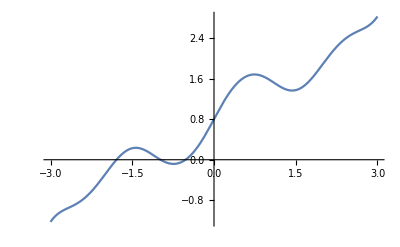

```mathematica
f[x_]:= Sin[x Cos[x+ArcTan[x]]]+ 0.8+ x
Plot[f[x],{x,-3,3}]
```

```mathematica
x0=0.8;
{xVal,fRes}={x,f[x]}/.FindRoot[f[x]==0,{x, x0}];
xk=x0;
TableForm[
Data=Table[
xk=xk-f[xk]/f'[xk];
{xk,xk-xVal,Abs[f[xk]]},{20}],
TableHeadings->{Automatic,{"x_k","||x_k-xVal||","|f[x_k]|"}}]
```

| x_k | ||x_k-xVal|| | |f[x_k]|
1 | 9.98856 | 10.5119 | 9.81775
2 | 17.7128 | 18.2361 | 17.8263
3 | 14.2096 | 14.733 | 14.0123
4 | 1.11512 | 1.63843 | 1.50932
5 | 3.24519 | 3.7685 | 3.45619
6 | 2.29541 | 2.81872 | 2.27723
7 | 0.176255 | 0.699563 | 1.14103
8 | -0.454623 | 0.0686848 | 0.0601891
9 | -0.515121 | 0.00818644 | 0.00631308
10 | -0.523159 | 0.000149107 | 0.00011289
11 | -0.523308 | 5.13572×10^-8 | 3.88696×10^-8
12 | -0.523308 | 6.10623×10^-15 | 4.55191×10^-15
13 | -0.523308 | 1.11022×10^-16 | 0.
14 | -0.523308 | 1.11022×10^-16 | 0.
15 | -0.523308 | 1.11022×10^-16 | 0.
16 | -0.523308 | 1.11022×10^-16 | 0.
17 | -0.523308 | 1.11022×10^-16 | 0.
18 | -0.523308 | 1.11022×10^-16 | 0.
19 | -0.523308 | 1.11022×10^-16 | 0.
20 | -0.523308 | 1.11022×10^-16 | 0.

### 2D Newton

Can not resist that the same Newton formula works in more than 1D!

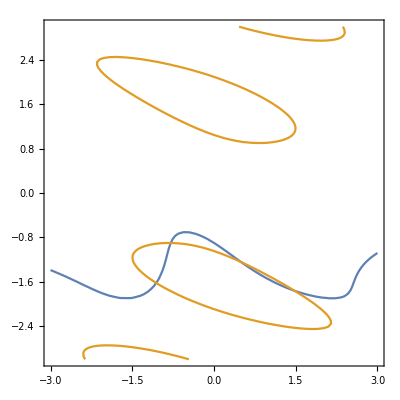

```mathematica
Clear[f,x,y]
f[{x_,y_}]:= {Sin[x Cos[y+ArcTan[x]]]+ 0.9+ y, x^2 + 2 y Sin[x+3y]}
df[{x_,y_}]= D[f[{x,y}],{{x,y}}];
ContourPlot[{f[{x,y}]⟦1⟧==0,f[{x,y}]⟦2⟧==0},{x,-3,3},{y,-3,3},ContourShading->False]
```

```mathematica
x0={-1.622,0.84};
{xVal,fRes}={{x,y},f[{x,y}]}/.FindRoot[f[{x,y}]==0,{{x,y},x0}ᵀ ];
xk=x0;
TableForm[
Data=Table[
xk=xk-LinearSolve[df[xk],f[xk]];
{Norm[xk-xVal],Norm[f[xk]]},{20}],
TableHeadings->{Automatic,{"||x_k-xVal||","||f[x_k]||"}}]
```

| ||x_k-xVal|| | ||f[x_k]||
1 | 2.32801 | 1.74926
2 | 0.645938 | 0.378721
3 | 5.92288 | 43.2541
4 | 2.98642 | 7.06194
5 | 1.69019 | 1.46165
6 | 1.25408 | 0.173456
7 | 1.12351 | 0.0130927
8 | 1.10877 | 0.00016065
9 | 1.10857 | 2.85656×10^-8
10 | 1.10857 | 4.96507×10^-16
11 | 1.10857 | 4.96507×10^-16
12 | 1.10857 | 2.22045×10^-16
13 | 1.10857 | 1.79018×10^-15
14 | 1.10857 | 1.77636×10^-15
15 | 1.10857 | 2.22045×10^-16
16 | 1.10857 | 1.79018×10^-15
17 | 1.10857 | 1.77636×10^-15
18 | 1.10857 | 2.22045×10^-16
19 | 1.10857 | 1.79018×10^-15
20 | 1.10857 | 1.77636×10^-15

### Bisection Method

If I want to solve 
	f(x)=0
then I can bracket the root in an interval (a_k,b_k)  with f(a_k)f(b_k)<0 and we are going to preserve this property as follows.  Evaluate f((a_k+b_k)/2) and relace the appropriate endpoint by (a_k+b_k)/2.

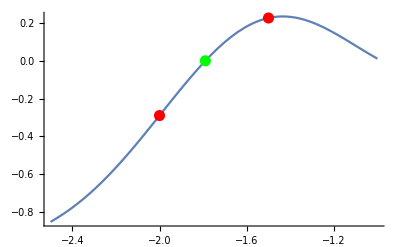

```mathematica
Clear[BisectionStep,f]
BisectionStep[f_][{{a_,b_},{fa_,fb_}}]:= Module[{z=0.5*(a+b),fz},
fz=f[z];  
If[ f[z]*fa>0, {{z,b},{fz,fb}}, {{a,z},{fa,fz}}]
]

f[x_]:= Sin[x Cos[x+ArcTan[x]]]+ 0.8+ x
{a,b}={-2,-1.5};
{xVal,fVal}={x,f[x]}/.FindRoot[f[x]==0,{x, a}];
{fa,fb}={f[a],f[b]};
Plot[f[x],{x,-2.5,-1},Epilog->{PointSize[0.02],
{Red,Point[{a,fa}],Point[{b,fb}]},
{Green,Point[{xVal,f[xVal]}]}}
]
```

```mathematica
{{ak,bk},{fak,fbk}}={{a,b},{fa,fb}};
BisectionData=Table[
{{ak,bk},{fak,fbk}}=BisectionStep[f][{{ak,bk},{fak,fbk}}];
{ak-xVal,bk-xVal,fak, fbk},{20}];
TableForm[BisectionData,
TableHeadings->{Automatic,{"a_k-xVal","b_k-xVal","f[a_k]","f[b_k]"}}]
```

| a_k-xVal | b_k-xVal | f[a_k] | f[b_k]
1 | -0.210323 | 0.039677 | -0.29021 | 0.0468765
2 | -0.085323 | 0.039677 | -0.111751 | 0.0468765
3 | -0.022823 | 0.039677 | -0.0285906 | 0.0468765
4 | -0.022823 | 0.00842702 | -0.0285906 | 0.010271
5 | -0.00719798 | 0.00842702 | -0.00889817 | 0.010271
6 | -0.00719798 | 0.000614517 | -0.00889817 | 0.000754391
7 | -0.00329173 | 0.000614517 | -0.00405521 | 0.000754391
8 | -0.00133861 | 0.000614517 | -0.0016462 | 0.000754391
9 | -0.000362046 | 0.000614517 | -0.000444847 | 0.000754391
10 | -0.000362046 | 0.000126235 | -0.000444847 | 0.000155037
11 | -0.000117905 | 0.000126235 | -0.000144839 | 0.000155037
12 | -0.000117905 | 4.16498×10^-6 | -0.000144839 | 5.11582×10^-6
13 | -0.0000568702 | 4.16498×10^-6 | -0.0000698572 | 5.11582×10^-6
14 | -0.0000263526 | 4.16498×10^-6 | -0.0000323697 | 5.11582×10^-6
15 | -0.0000110938 | 4.16498×10^-6 | -0.0000136267 | 5.11582×10^-6
16 | -3.46442×10^-6 | 4.16498×10^-6 | -4.25536×10^-6 | 5.11582×10^-6
17 | -3.46442×10^-6 | 3.50281×10^-7 | -4.25536×10^-6 | 4.3025×10^-7
18 | -1.55707×10^-6 | 3.50281×10^-7 | -1.91255×10^-6 | 4.3025×10^-7
19 | -6.03393×10^-7 | 3.50281×10^-7 | -7.41148×10^-7 | 4.3025×10^-7
20 | -1.26556×10^-7 | 3.50281×10^-7 | -1.55449×10^-7 | 4.3025×10^-7

Looking at the convergences

```mathematica
ConvData=Abs[BisectionData⟦All,3⟧];
TabView[{
"Data"->ListPlot[ConvData],
"LogData"->ListLogPlot[ConvData],
"Ratios"->ListLogPlot[ConvData⟦2;;-1⟧/ConvData⟦1;;-2⟧,PlotRange->All]
}]
```

123

## Secant Method: 1D

If I want to solve 
	f(x)=0
then I can bracket the root in an interval (a_k,b_k)  with f(a_k)f(b_k)<0 and we are going to preserve this property as follows.  Evaluate f((a_k+b_k)/2) and relace the appropriate endpoint by (a_k+b_k)/2.

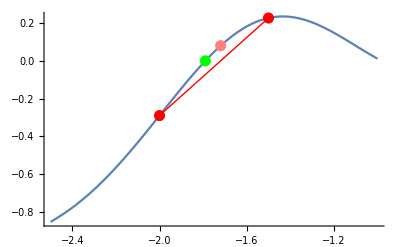

```mathematica
Clear[SecantStep,f]
SecantStep[f_][{{a_,b_},{fa_,fb_}}]:= Module[
{z=(b*fa-a*fb)/(fa-fb),fz},
fz=f[z];  
If[ f[z]*fa>0, {{z,b},{fz,fb}}, {{a,z},{fa,fz}}]
]

f[x_]:= Sin[x Cos[x+ArcTan[x]]]+ 0.8+ x
{a,b}={-2,-1.5};
{xVal,fVal}={x,f[x]}/.FindRoot[f[x]==0,{x, a}];
{fa,fb}={f[a],f[b]};
z=(b*fa-a*fb)/(fa-fb);
fz=f[z];
Plot[f[x],{x,-2.5,-1},Epilog->{PointSize[0.02],
{Red,Point[{a,fa}],Point[{b,fb}],Line[{{a,fa},{b,fb}}]},
{Pink, Point[{z,fz}]},
{Green,Point[{xVal,f[xVal]}]}}
]
```

```mathematica
{{ak,bk},{fak,fbk}}={{a,b},{fa,fb}};
Data=Table[
{{ak,bk},{fak,fbk}}=SecantStep[f][{{ak,bk},{fak,fbk}}];
{ak-xVal,bk-xVal,fak, fbk},{16}];
TableForm[Data,
TableHeadings->{Automatic,{"a_k-xVal","b_k-xVal","f[a_k]","f[b_k]"}}]
```

| a_k-xVal | b_k-xVal | f[a_k] | f[b_k]
1 | -0.210323 | 0.0702793 | -0.29021 | 0.0802349
2 | -0.210323 | 0.00950339 | -0.29021 | 0.0115712
3 | -0.210323 | 0.0010746 | -0.29021 | 0.00131864
4 | -0.210323 | 0.000118402 | -0.29021 | 0.000145418
5 | -0.210323 | 0.0000130073 | -0.29021 | 0.0000159766
6 | -0.210323 | 1.42847×10^-6 | -0.29021 | 1.75459×10^-6
7 | -0.210323 | 1.5687×10^-7 | -0.29021 | 1.92684×10^-7
8 | -0.210323 | 1.7227×10^-8 | -0.29021 | 2.11599×10^-8
9 | -0.210323 | 1.89181×10^-9 | -0.29021 | 2.32371×10^-9
10 | -0.210323 | 2.07752×10^-10 | -0.29021 | 2.55181×10^-10
11 | -0.210323 | 2.28146×10^-11 | -0.29021 | 2.80234×10^-11
12 | -0.210323 | 2.50555×10^-12 | -0.29021 | 3.07754×10^-12
13 | -0.210323 | 2.75113×10^-13 | -0.29021 | 3.37952×10^-13
14 | -0.210323 | 3.04201×10^-14 | -0.29021 | 3.75255×10^-14
15 | -0.210323 | 3.10862×10^-15 | -0.29021 | 3.77476×10^-15
16 | -0.210323 | 4.44089×10^-16 | -0.29021 | 4.44089×10^-16

Looking at the convergences

```mathematica
ConvData=Abs[Data⟦All,4⟧];
TabView[{
"Data"->ListPlot[ConvData],
"LogData"->ListLogPlot[ConvData],
"Ratios"->ListLogPlot[ConvData⟦2;;-1⟧/ConvData⟦1;;-2⟧,PlotRange->All]
}]
```

123

## Conclusions

Newton converges faster than is needed. Bisection converges too slowly to be useful.  The secant method converges fast enough to be useful!  We will look at a multi dimensional “secant” like solver based on the SR1 Quasi-Newton update.